## Ray trajectories -- resulting pdf

Started 10/06/2015
Ignoring diffusive term in the FPE, I find the steady state PDF in the wall region and investigate its peak.

Derived trajectory and PDFs

```mathematica
Δξ[θ_,θ0_]:=Log[θ/θ0]-θ+θ0
θ0[θ_,Δ_?NumericQ]:=θ0/.FindRoot[Δξ[θ,θ0]==Δ,{θ0,1+θ}]//Re//Quiet
p0[θ0_,β_]:=√(β/(2π))Exp[-β/2 θ0^2]HeavisideTheta[θ0-1]
(* ρ is 2D PDF; pθ is marginalised over Δ *)
ρ[θ_,θ0_?NumericQ,β_?NumericQ]:=√((1-θ0)^2+θ0^2)θ0/(θ0-1)(θ-1)^2/(2 θ^2-2θ+1)*p0[θ0,β]//Re
pθ[θ_?NumericQ,β_?NumericQ]:=NIntegrate[ρ[θ,θ0[θ,δ],β],{δ,0,1}]
```

PDFs in 2D and 1D for β=1

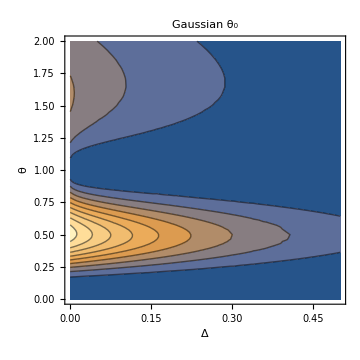

```mathematica
ContourPlot[ρ[θ,θ0[θ,δ],1.0],
{δ,0,0.5},{θ,0,2},
PlotRange->All,
PlotLabel->Style["Gaussian θ_0",Bold,FontSize->16],
FrameLabel->{Style["Δ",Bold,FontSize->16],Style["θ",Bold,FontSize->16]},
FrameTicksStyle->14,
ImageSize->Medium]
```

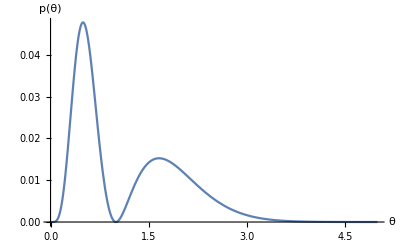

```mathematica
Plot[
{pθ[θ,1.0]},
{θ,0.01,5},
PlotRange->{{0,Automatic},All},
AxesLabel->{"θ","p(θ)"}]
```

Behaviour of maximum with β

```mathematica
bmin=0.1;bmax=10.0;db=0.5;
blist=Table[b,{b,bmin,bmax,db}];
θmax=Table[
FindMaximum[pθ[θ,b],{θ,0.51+0.14Log[b]}]//Quiet,
{b,bmin,bmax,db}];
```

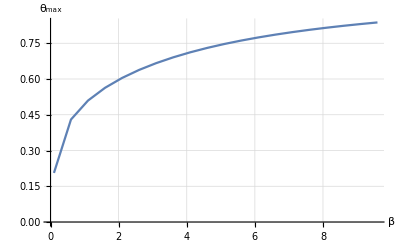

```mathematica
θmaxplt=ListLinePlot[Transpose[{blist,θ/.Transpose[θmax][[2]]}],
PlotRange->{{0,All},{0,All}},
AxesLabel->{"β","θ_max"},
GridLines->Automatic]
```

```mathematica
lblist=Table[Log[b],{b,bmin,bmax,db}];
lθmax=Table[
FindMaximum[pθ[θ,b],{θ,0.51+0.14Log[b]}]//Quiet,
{b,bmin,bmax,db}];
ldat=Transpose[{lblist,θ/.Transpose[lθmax][[2]]}];
```

0.510923+0.142956 x

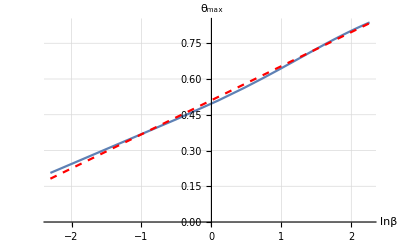

```mathematica
lθmaxfit=Fit[ldat,{1,x},x]
lθmaxplt=ListLinePlot[ldat,
PlotRange->Automatic,
AxesLabel->{"lnβ","θ_max"},GridLines->Automatic];
Show[lθmaxplt,Plot[lθmaxfit,{x,Log[bmin],Log[bmax]},PlotStyle->{Red,Dashed}]]
```

```mathematica
bmin=10;bmax=100;db=1;
lblist=Table[Log[b],{b,bmin,bmax,db}];
lθmax=Table[
FindMaximum[pθ[θ,b],{θ,0.503+0.142Log[b]}]//Quiet,
{b,bmin,bmax,db}];
ldat=Transpose[{lblist,θ/.Transpose[lθmax][[2]]}];
```

0.502979+0.1416 x

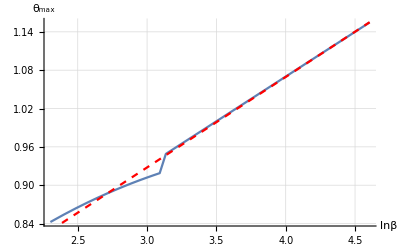

```mathematica
lθmaxfit=Fit[ldat,{1,x},x]
lθmaxplt=ListLinePlot[ldat,
PlotRange->Automatic,
AxesLabel->{"lnβ","θ_max"},GridLines->Automatic];
Show[lθmaxplt,Plot[lθmaxfit,{x,Log[bmin],Log[bmax]},PlotStyle->{Red,Dashed}]]
```